```mathematica
map=Map[Characters,{
"0000222222220000", 
"1              0",
"1      11111   0",
"1     0        0",
"0     0  1110000",
"0     3        0",
"0   10000      0",
"0   0   11100  0",
"0   0   0      0",
"0   0   1  00000",
"0       1      0",
"2       1      0",
"0       0      0",
"0 0000000      0",
"0              0", 
"0002222222200000"
}];
replaceRules = {" "->0,"0"->1,"1"->2,"2"->3};
```

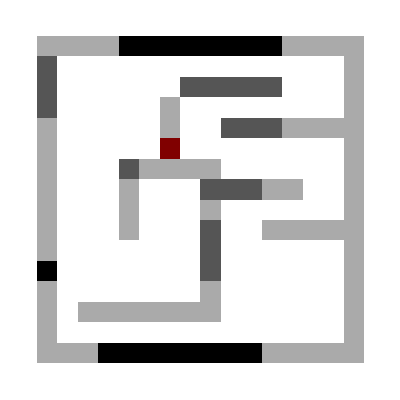

```mathematica
ArrayPlot[map/.replaceRules]
```